# Setup

```mathematica
(* ================================================================ *)
(* MODULE 0: SETUP                                                  *)
(* ================================================================ *)

baseDir = NotebookDirectory[];
Get[FileNameJoin[{baseDir, "QKT_full.wl"}]];
$HistoryLength = 0;
EnsureDir[dir_] := If[!DirectoryQ[dir],
  CreateDirectory[dir, CreateIntermediateDirectories -> True]];
kStr[k_] := StringReplace[
  If[StringEndsQ[#, "."], # <> "0", #] &[ToString[N[k]]], "." -> "_"];
```

```mathematica
LaunchKernels[14];
```

# Kicked ising

```mathematica
Off[MakeExpression::boxfmt]

(* ============================================================ *)
(*  Mixed-Field Ising Model — Floquet texture test               *)
(* ============================================================ *)

L  = 10;            (* number of spins, dim = 2^L = 1024 *)
J  = 1.0;
hz = 0.8090;        (* Kim-Huse chaotic parameters *)
hx = 0.9045;
tau = 1.0;
dim = 2^L;
```

```mathematica
(* Pauli matrices *)
Id2 = IdentityMatrix[2];
sx  = {{0, 1}, {1, 0}};
sz  = {{1, 0}, {0, -1}};

(* Single-site operator embedded in the L-site space *)
op[mat_, i_, len_] := 
  KroneckerProduct @@ Table[If[k == i, mat, Id2], {k, 1, len}];

(* Diagonal part: Ising + longitudinal field, open BC *)
Hz = -J Sum[op[sz, i, L] . op[sz, i + 1, L], {i, 1, L - 1}]- hz Sum[op[sz, i, L], {i, 1, L}];

(* Off-diagonal part: transverse field *)
Hx = -hx Sum[op[sx, i, L], {i, 1, L}];
```

```mathematica
diagHz   = Normal[Diagonal[Hz]];
expHz    = DiagonalMatrix[Exp[-I tau diagHz]];
sqrtHz   = DiagonalMatrix[Exp[-I tau diagHz/2]];
expHx    = MatrixExp[-I tau Hx];

UF    = expHz . expHx;
UFsym = sqrtHz . expHx . sqrtHz;
```

```mathematica
{eval1, vec1} = Eigensystem[UF];
{eval2, vec2} = Eigensystem[UFsym];
```

```mathematica
vec1[[1]][[1;;-1;;50]]//Im//Chop
```

{0,-0.00632292,-0.108334,0,0.0184299,0.0142525}

```mathematica
vec2[[1]][[1;;-1;;50]]//Im//Chop
```

{0,0,0,0,0,0}

```mathematica
f1 = ConstantArray[1./Sqrt[dim], dim];

P1 = Abs[vec1 . f1]^2;
P2 = Abs[vec2 . f1]^2;

sat1 = dim * Total[P1^2];
sat2 = dim * Total[P2^2];
```

```mathematica
Print["Asymmetric U_F  :  Σ∞ = ", sat1, "   (expect ~2, CUE-like)"];
Print["Symmetric U_F   :  Σ∞ = ", sat2, "   (expect ~3, COE)"];

(* Optional sanity check: maximum imaginary component of UFsym eigenvectors *)
Print["max |Im(vec_sym)| = ", Max[Abs[Im[vec2]]],
      "   (should be ~ machine epsilon up to a global phase)"];
```

Asymmetric U_F  :  Σ∞ = 6.61063   (expect ~2, CUE-like)

Symmetric U_F   :  Σ∞ = 6.30865   (expect ~3, COE)

max |Im(vec_sym)| = 8.31626×10^-14   (should be ~ machine epsilon up to a global phase)

## Change of basis

```mathematica
gaugeSweep[theta_] := Module[{D, U, V, P},
  D = DiagonalMatrix[Exp[-I theta diagHz]];
  U = D . UFsym . ConjugateTranspose[D];
  V = Eigenvectors[U];
  P = Abs[V . f1]^2;
  dim * Total[P^2]
];
```

```mathematica
sweep = Table[{theta, gaugeSweep[theta]}, {theta, 0, tau/2, tau/40}];
```

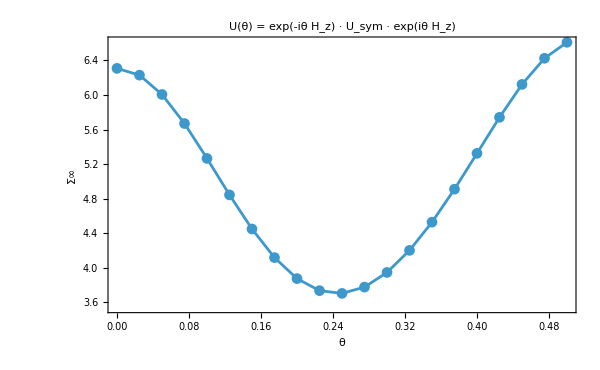

```mathematica
ListLinePlot[sweep,
  PlotMarkers -> Automatic,
  Frame -> True,
  FrameLabel -> {"θ", "Σ∞"},
  GridLines -> {None, {2, 3}},
  PlotRange -> All,
  PlotLabel -> "U(θ) = exp(-iθ H_z) · U_sym · exp(iθ H_z)",
  ImageSize -> 600
]
```

```mathematica
sweep
```

{{0.,6.30865},{0.025,6.23016},{0.05,6.00644},{0.075,5.66978},{0.1,5.26565},{0.125,4.8434},{0.15,4.44837},{0.175,4.11684},{0.2,3.87403},{0.225,3.73431},{0.25,3.70245},{0.275,3.77557},{0.3,3.94543},{0.325,4.2006},{0.35,4.5275},{0.375,4.90947},{0.4,5.3243},{0.425,5.74163},{0.45,6.12286},{0.475,6.42532},{0.5,6.61063}}

## Entanglement

```mathematica
EntanglementEntropySVD[psi_, dA_, dB_] :=
  Module[{mat, sv2},
    mat = ArrayReshape[psi, {dA, dB}];
    sv2 = SingularValueList[mat]^2;
    (* Hard threshold at machine epsilon level *)
    sv2 = Select[sv2, # > 1.*^-14 &];
    (* Renormalize to absorb discarded numerical noise *)
    sv2 = sv2 / Total[sv2];
    -sv2 . Log[sv2]
  ]
```

```mathematica
entanglement=ParallelTable[EntanglementEntropySVD[i, L/2,L/2 ],{i,vec1}];
```

```mathematica
entanglement2=ParallelTable[EntanglementEntropySVD[i, L/2,L/2 ],{i,vec2}];
```

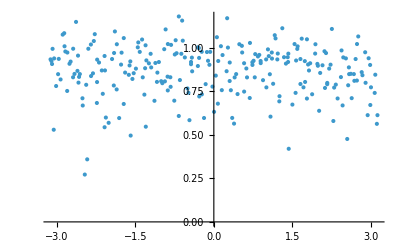

```mathematica
ListPlot[Transpose[{Arg[eval1],entanglement}],PlotRange->All]
```

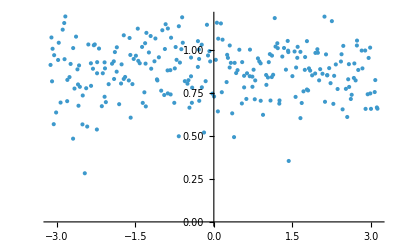

```mathematica
ListPlot[Transpose[{Arg[eval2],entanglement2}],PlotRange->All]
```

```mathematica
PageEntropy[La_,Lb_]:=N[PolyGamma[0,2^La*2^Lb+1]-PolyGamma[0,2^Lb+1]-(2^La-1)/(2*2^Lb)]
```

```mathematica
La=4;
Lb=4;
```

```mathematica
PageEntropy[La,Lb]//N
```

2.27487

```mathematica
Print["dA, dB = ",{2^La,2^Lb}];
Print["Max possible entropy = ",N[Log[Min[2^La,2^Lb]]]];
Print["Page value = ",PageEntropy[La,Lb]];
```

dA, dB = {16,16}

Max possible entropy = 2.77259

Page value = 2.27487

```mathematica
Print["Mean Schmidt rank: ",Mean[Length[Select[SingularValueList[ArrayReshape[#,{2^La,2^Lb}]]^2,#>10^-14&]]&/@vec1]];
```

Mean Schmidt rank: 16

```mathematica
phases=Mod[Arg[eval1],2 Pi];
spacings=Differences[Sort[phases]];
ratios=Min[#1/#2,#2/#1]&@@@Partition[spacings,2,1];
Mean[ratios]
```

0.416354

```mathematica
{J,hz,hx,tau} (*print these to verify*)
```

{1.,0.809,0.9045,1.}

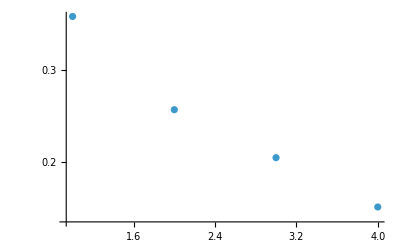

```mathematica
sv=SingularValueList[ArrayReshape[vec1[[1]],{64,64}]];
ListLogPlot[sv^2,PlotRange->All]
```

```mathematica
"C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Spectral measures analysis\\qkt texture.nb"
```

# sectors

```mathematica
(* ============================================================ *)
(*  Reflection-sector diagonalization                            *)
(* ============================================================ *)

(* Build orthonormal bases for P=±1 sectors explicitly *)
buildSectorBases[L_] := Module[
  {dim = 2^L, refl, evenB = {}, oddB = {}, seen, r},
  refl[k_] := FromDigits[Reverse[IntegerDigits[k - 1, 2, L]], 2] + 1;
  seen = ConstantArray[False, dim];
  Do[
    If[! seen[[i]],
     r = refl[i];
     seen[[i]] = True; seen[[r]] = True;
     If[i == r,
      AppendTo[evenB, SparseArray[{i -> 1.}, dim]],
      AppendTo[evenB, SparseArray[{i -> 1./Sqrt[2.], r -> 1./Sqrt[2.]}, dim]];
      AppendTo[oddB,  SparseArray[{i -> 1./Sqrt[2.], r -> -1./Sqrt[2.]}, dim]]
      ]
     ], {i, dim}];
  <|"Even" -> Normal /@ evenB, "Odd" -> Normal /@ oddB|>
];

bases = buildSectorBases[L];
BE = bases["Even"];   (* dE × dim *)
BO = bases["Odd"];    (* dO × dim *)
dE = Length[BE]; dO = Length[BO];

(* Project Floquet operators (basis is real, so Transpose = ConjugateTranspose) *)
UFe  = BE . UF . Transpose[BE];
UFo  = BO . UF . Transpose[BO];
UFse = BE . UFsym . Transpose[BE];
UFso = BO . UFsym . Transpose[BO];

{evalE,  vecE}  = Eigensystem[UFe];
{evalO,  vecO}  = Eigensystem[UFo];
{evalSE, vecSE} = Eigensystem[UFse];
{evalSO, vecSO} = Eigensystem[UFso];

(* Re-expand sector eigenvectors into the full 2^L computational basis *)
vecEfull  = vecE  . BE;
vecOfull  = vecO  . BO;
vecSEfull = vecSE . BE;
vecSOfull = vecSO . BO;
```

```mathematica
(* Sanity checks *)
Print["Sector dims: even = ", dE, ", odd = ", dO, ", total = ", dE + dO];

phasesE = Mod[Arg[evalE], 2 Pi];
ratiosE = Min[#1/#2, #2/#1] & @@@ 
   Partition[Differences[Sort[phasesE]], 2, 1];
Print["<r> in even sector = ", Mean[ratiosE], " (expect ~0.527 for COE)"];

(* Entanglement in even sector *)
entEven = ParallelTable[EntanglementEntropySVD[v, 2^La, 2^Lb], {v, vecEfull}];
Print["Mean entanglement (even sector) = ", Mean[entEven],
      "   Page = ", PageEntropy[La, Lb]];
```

Sector dims: even = 528, odd = 496, total = 1024

<r> in even sector = 0.535225 (expect ~0.527 for COE)

Mean entanglement (even sector) = 2.21113   Page = 2.27487

```mathematica
(* Sanity checks *)
Print["Sector dims: even = ", dE, ", odd = ", dO, ", total = ", dE + dO];

phasesO = Mod[Arg[evalO], 2 Pi];
ratiosO = Min[#1/#2, #2/#1] & @@@ 
   Partition[Differences[Sort[phasesO]], 2, 1];
Print["<r> in even sector = ", Mean[ratiosE], " (expect ~0.527 for COE)"];

(* Entanglement in even sector *)
entOdd = ParallelTable[EntanglementEntropySVD[v, 2^La, 2^Lb], {v, vecSOfull}];
Print["Mean entanglement (even sector) = ", Mean[entOdd],
      "   Page = ", PageEntropy[La, Lb]];
```

Sector dims: even = 528, odd = 496, total = 1024

<r> in even sector = 0.535225 (expect ~0.527 for COE)

Mean entanglement (even sector) = 2.21669   Page = 2.27487

```mathematica
(* Compute entanglement for all four sector-operator combinations *)
entUFe  = ParallelTable[EntanglementEntropySVD[v, 2^La, 2^Lb], {v, vecEfull}];
entUFo  = ParallelTable[EntanglementEntropySVD[v, 2^La, 2^Lb], {v, vecOfull}];
entSyme = ParallelTable[EntanglementEntropySVD[v, 2^La, 2^Lb], {v, vecSEfull}];
entSymo = ParallelTable[EntanglementEntropySVD[v, 2^La, 2^Lb], {v, vecSOfull}];

pageVal = PageEntropy[La, Lb];
```

```mathematica
pageVal
```

2.27487

```mathematica
(* Asymmetric UF *)
pUF = ListPlot[
  {Transpose[{Arg[evalE], entUFe}],
   Transpose[{Arg[evalO], entUFo}]},
  PlotRange -> All, Frame -> True,
  FrameLabel -> {"Quasienergy", "S"},
  PlotLegends -> {"Even", "Odd"},
  PlotStyle -> {Directive[Blue, Opacity[0.4], PointSize[0.005]],
                Directive[Red,  Opacity[0.4], PointSize[0.005]]},
  GridLines -> {None, {pageVal}},
  GridLinesStyle -> Directive[Black, Dashed],
  PlotLabel -> Style["Asymmetric U_F", 14, Black],
  ImageSize -> 600
];

(* Symmetric UFsym *)
pSym = ListPlot[
  {Transpose[{Arg[evalSE], entSyme}],
   Transpose[{Arg[evalSO], entSymo}]},
  PlotRange -> All,
 Frame -> True,
  FrameLabel -> {"Quasienergy", "S"},
  PlotLegends -> {"Even", "Odd"},
  PlotStyle -> {Directive[Blue, Opacity[0.4], PointSize[0.005]],
                Directive[Red,  Opacity[0.4], PointSize[0.005]]},
  GridLines -> {None, {pageVal}},
  GridLinesStyle -> Directive[Black, Dashed],
  PlotLabel -> Style["Symmetric U_F", 14, Black],
  ImageSize -> 600
];

GraphicsColumn[{pUF, pSym}, Spacings -> 20]
```

-Graphics-

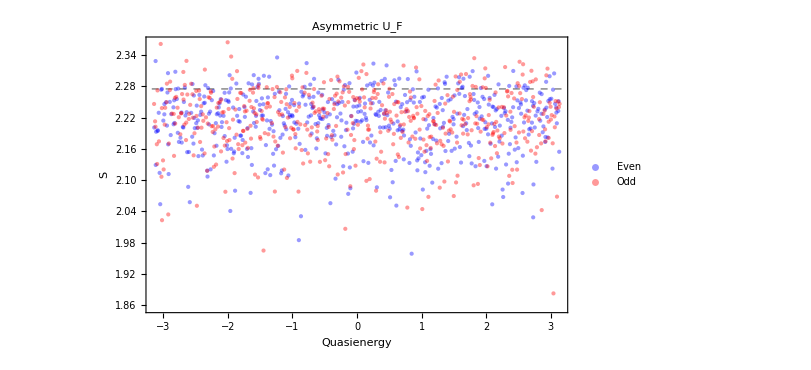

```mathematica
pUF
```

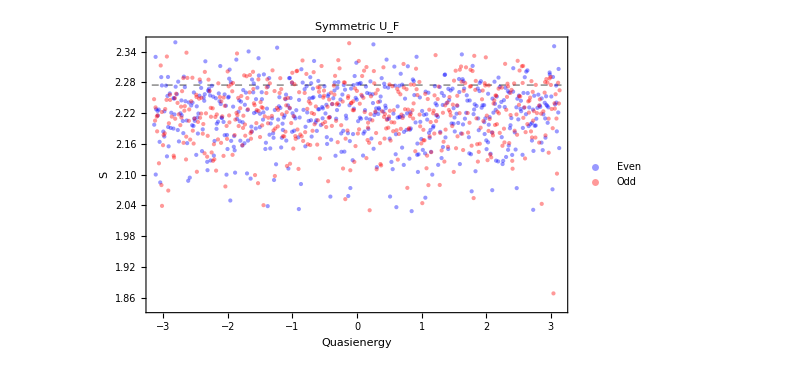

```mathematica
pSym
```

```mathematica
(* ============================================================ *)
(*  Kicked Ising — Ensemble for Texture and SFF                  *)
(* ============================================================ *)

nEns    = 50;
hxCenter = 0.9045;
delta   = 0.005;
hxList  = RandomReal[{hxCenter - delta, hxCenter + delta}, nEns];

(* Build sector bases once — fixed for all realizations *)
bases = buildSectorBases[L];
BE = bases["Even"];
BO = bases["Odd"];
dE = Length[BE];
dO = Length[BO];

(* Uniform textureless state within each sector *)
f1E = ConstantArray[1./Sqrt[dE], dE];
f1O = ConstantArray[1./Sqrt[dO], dO];

(* ------------------------------------------------------------ *)
(*  Single-realization eigensystem within sectors               *)
(* ------------------------------------------------------------ *)

GetKIEigensystem[hx_] := Module[
  {Hxloc, expHxloc, UFloc, UFeloc, UFoloc, esE, esO, phE, phO},
  Hxloc    = -hx Sum[op[sx, i, L], {i, 1, L}];
  expHxloc = MatrixExp[-I tau Hxloc];
  UFloc    = expHz . expHxloc;         (* expHz fixed *)
  UFeloc   = BE . UFloc . Transpose[BE];
  UFoloc   = BO . UFloc . Transpose[BO];
  esE = Eigensystem[UFeloc];
  esO = Eigensystem[UFoloc];
  phE = Sort[Mod[Arg[esE[[1]]], 2 Pi]];
  phO = Sort[Mod[Arg[esO[[1]]], 2 Pi]];
  <|"Even" -> <|"Phases" -> phE, "Vectors" -> esE[[2, Ordering[phE]]]|>,
    "Odd"  -> <|"Phases" -> phO, "Vectors" -> esO[[2, Ordering[phO]]]|>|>
];

(* ------------------------------------------------------------ *)
(*  Generate ensemble                                            *)
(* ------------------------------------------------------------ *)

DistributeDefinitions[GetKIEigensystem, buildSectorBases,
  expHz, BE, BO, op, sz, sx, Id2, J, hz, tau, L];

Print["Generating ", nEns, " realizations..."];
rawEns = ParallelTable[GetKIEigensystem[hx], {hx, hxList},
  Method -> "CoarsestGrained"];

(* Structure ensemble per sector *)
kiEnsemble = <|
  "Even" -> Table[<|"Phases" -> d["Even","Phases"],
                    "Vectors" -> d["Even","Vectors"]|>, {d, rawEns}],
  "Odd"  -> Table[<|"Phases" -> d["Odd","Phases"],
                    "Vectors" -> d["Odd","Vectors"]|>, {d, rawEns}]|>;

(* ------------------------------------------------------------ *)
(*  Texture                                                      *)
(* ------------------------------------------------------------ *)

tMaxTex = 1000;
sigmaSm = 5;

EnsembleTexSector[ensembleList_, f1_, tMax_] := Module[
  {nMat = Length[ensembleList], tGrid = Range[0, tMax], allTex},
  DistributeDefinitions[tGrid, f1];
  allTex = ParallelTable[
    Module[{ph = ensembleList[[i,"Phases"]], vecs = ensembleList[[i,"Vectors"]], 
            d, pArr},
      d = Length[ph];
      pArr = Abs[vecs . f1]^2;
      Table[d * Abs[Total[pArr * Exp[-I t ph]]]^2, {t, tGrid}]
    ], {i, nMat}, Method -> "CoarsestGrained"];
  <|"Time" -> tGrid, "AllTex" -> allTex, "MeanTex" -> Mean[allTex]|>
];

Print["Computing texture — Even sector..."];
texE = EnsembleTexSector[kiEnsemble["Even"], f1E, tMaxTex];
Print["Computing texture — Odd sector..."];
texO = EnsembleTexSector[kiEnsemble["Odd"],  f1O, tMaxTex];

texEsm = Mean[Map[GaussianFilter[#, sigmaSm]&, texE["AllTex"]]];
texOsm = Mean[Map[GaussianFilter[#, sigmaSm]&, texO["AllTex"]]];

(* ------------------------------------------------------------ *)
(*  Spectral Form Factor                                         *)
(* ------------------------------------------------------------ *)

tauMax = 1.0;
nPts   = 500;

kiSpectraE = Table[
  UnfoldLinear[kiEnsemble["Even"][[i, "Phases"]]], {i, nEns}];
kiSpectraO = Table[
  UnfoldLinear[kiEnsemble["Odd"][[i,  "Phases"]]], {i, nEns}];

sffE = EnsembleSFF[kiSpectraE, tauMax, nPts];
sffO = EnsembleSFF[kiSpectraO, tauMax, nPts];
```

Generating 50 realizations...

Computing texture — Even sector...

Computing texture — Odd sector...

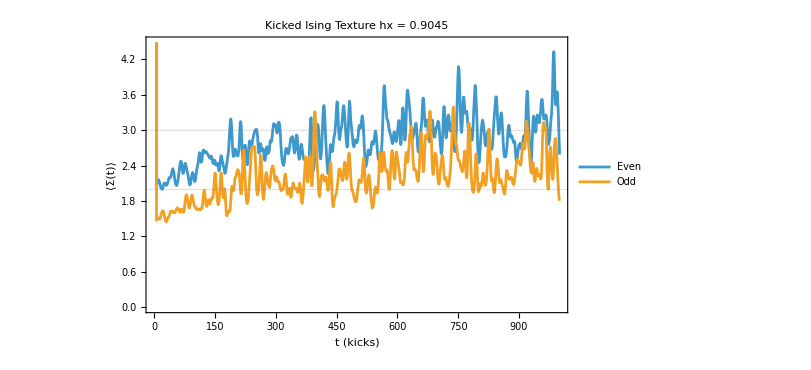

```mathematica
ListLinePlot[
  {Transpose[{texE["Time"], texEsm}],
   Transpose[{texO["Time"], texOsm}]},
  PlotLegends -> {"Even", "Odd"},
  FrameLabel -> {"t (kicks)", "⟨Σ(t)⟩"},
  GridLines -> {None, {2, 3}},
  Frame -> True, ImageSize -> 600,
  PlotLabel -> Style["Kicked Ising Texture  hx = " <> ToString[hxCenter], 14]
]
```

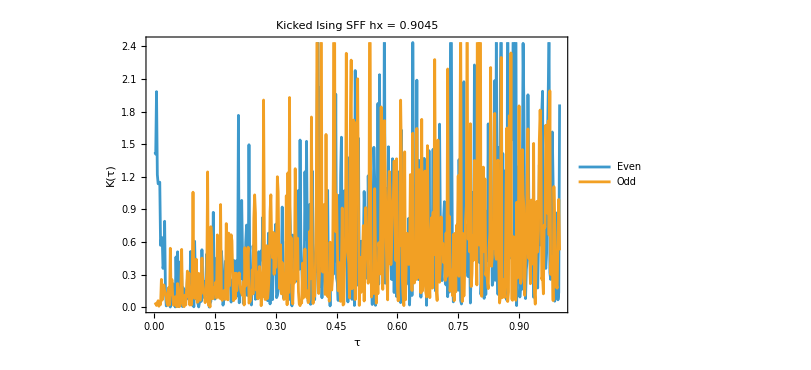

```mathematica
ListPlot[
  {Transpose[{sffE["Tau"], sffE["MeanK"]}],
   Transpose[{sffO["Tau"], sffO["MeanK"]}]},
  PlotLegends -> {"Even", "Odd"},
  FrameLabel -> {"τ", "K(τ)"},
  Frame -> True, ImageSize -> 600,
Joined->True,
  PlotLabel -> Style["Kicked Ising SFF  hx = " <> ToString[hxCenter], 14]
]
```

```mathematica
computeAWedgeB[diagE_, tau_] := Module[
  {d = Length[diagE], phases, a, b},
  phases = tau * diagE / 2;
  a = Cos[phases] / Sqrt[d];
  b = Sin[phases] / Sqrt[d];
  Abs[a]^2 * Abs[b]^2 - (a . b)^2
];

awbE = computeAWedgeB[Diagonal[BE . DiagonalMatrix[diagHz] . Transpose[BE]], tau];
awbO = computeAWedgeB[Diagonal[BO . DiagonalMatrix[diagHz] . Transpose[BO]], tau];

Print["Even |a∧b|.b2 = ", awbE, "  → Σ∞ prediction = ", 3 - 4 awbE];
Print["Odd  |a∧b|.b2 = ", awbO, "  → Σ∞ prediction = ", 3 - 4 awbO];
```

Even |a∧b|.b2 = {-0.0000272221,-0.0000275321,-0.0000273792,-0.0000277042,-0.0000273792,-0.0000271906,-0.000027932,-0.0000276158,-0.0000273792,-0.0000271906,-0.000027932,-0.0000280853,-0.000027932,-0.0000280853,-0.0000273152,-0.0000276198,-0.0000273792,-0.0000271906,-0.000027932,-0.0000280853,-0.000027932,-0.0000275322,-0.0000273791,-0.0000271985,-0.000027932,-0.0000280853,-0.0000273791,-0.0000271985,-0.0000273152,-0.0000271985,-0.0000279905,-0.0000277002,-0.0000271906,-0.000027932,-0.0000280853,-0.000027932,-0.0000275322,-0.0000273791,-0.0000271985,-0.000027932,-0.0000275322,-0.0000280383,-0.0000277863,-0.0000273791,-0.0000277863,-0.0000278631,-0.0000280694,-0.000027932,-0.0000280853,-0.0000273791,-0.0000271985,-0.0000273791,-0.0000277863,-0.0000278631,-0.0000280694,-0.0000273152,-0.0000271985,-0.0000278631,-0.0000280694,-0.0000279905,-0.0000280694,-0.0000272627,-0.000027536,-0.0000271906,-0.000027932,-0.0000280853,-0.000027932,-0.0000275322,-0.0000273791,-0.0000271985,-0.000027932,-0.0000275322,-0.0000280383,-0.0000277863,-0.0000273791,-0.0000277863,-0.0000278631,-0.0000280694,-0.0000275322,-0.0000280383,-0.0000277863,-0.0000280383,-0.0000280365,-0.0000272221,-0.0000274523,-0.0000273791,-0.0000277863,-0.0000272221,-0.0000274523,-0.0000278631,-0.0000274523,-0.0000274523,-0.0000272221,-0.0000280853,-0.0000273791,-0.0000271985,-0.0000273791,-0.0000277863,-0.0000278631,-0.0000280694,-0.0000277863,-0.0000272221,-0.0000274523,-0.0000278631,-0.0000274523,-0.0000274523,-0.0000272221,-0.0000271985,-0.0000278631,-0.0000280694,-0.0000278631,-0.0000274523,-0.0000274523,-0.0000272221,-0.0000279905,-0.0000280694,-0.0000274523,-0.0000272221,-0.0000272627,-0.0000272221,-0.0000280365,-0.0000277825,-0.0000271906,-0.000027932,-0.0000280853,-0.000027932,-0.0000275322,-0.0000273791,-0.0000271985,-0.0000275322,-0.0000280383,-0.0000277863,-0.0000273791,-0.0000277863,-0.0000278631,-0.0000280694,-0.0000275322,-0.0000280383,-0.0000277863,-0.0000280383,-0.0000280365,-0.0000272221,-0.0000274523,-0.0000277863,-0.0000272221,-0.0000274523,-0.0000278631,-0.0000274523,-0.0000274523,-0.0000272221,-0.0000275322,-0.0000280383,-0.0000277863,-0.0000280365,-0.0000272221,-0.0000274523,-0.0000280365,-0.000027536,-0.0000272627,-0.0000272221,-0.0000272627,-0.0000280694,-0.0000278631,-0.0000277863,-0.0000272221,-0.0000274523,-0.0000272221,-0.0000272627,-0.0000280694,-0.0000278631,-0.0000274523,-0.0000280694,-0.0000278631,-0.0000274523,-0.0000278631,-0.0000277863,-0.0000280383,-0.0000280853,-0.0000273791,-0.0000271985,-0.0000277863,-0.0000278631,-0.0000280694,-0.0000277863,-0.0000272221,-0.0000274523,-0.0000278631,-0.0000274523,-0.0000274523,-0.0000272221,-0.0000277863,-0.0000272221,-0.0000274523,-0.0000272627,-0.0000280694,-0.0000278631,-0.0000274523,-0.0000280694,-0.0000278631,-0.0000274523,-0.0000278631,-0.0000277863,-0.0000280383,-0.0000271985,-0.0000278631,-0.0000280694,-0.0000274523,-0.0000274523,-0.0000272221,-0.0000274523,-0.0000280694,-0.0000278631,-0.0000278631,-0.0000277863,-0.0000280383,-0.0000280694,-0.0000274523,-0.0000272221,-0.0000278631,-0.0000277863,-0.0000280383,-0.0000272221,-0.0000277863,-0.0000280383,-0.0000280365,-0.0000280383,-0.0000272236,-0.0000274559,-0.0000271906,-0.000027932,-0.0000280853,-0.0000275322,-0.0000273791,-0.0000271985,-0.0000275322,-0.0000280383,-0.0000277863,-0.0000277863,-0.0000278631,-0.0000280694,-0.0000275322,-0.0000280383,-0.0000277863,-0.0000280365,-0.0000272221,-0.0000274523,-0.0000277863,-0.0000272221,-0.0000274523,-0.0000274523,-0.0000274523,-0.0000272221,-0.0000275322,-0.0000277863,-0.0000280365,-0.0000272221,-0.0000274523,-0.0000280365,-0.000027536,-0.0000272627,-0.0000272627,-0.0000280694,-0.0000278631,-0.0000277863,-0.0000272221,-0.0000274523,-0.0000272627,-0.0000280694,-0.0000278631,-0.0000274523,-0.0000280694,-0.0000278631,-0.0000278631,-0.0000277863,-0.0000280383,-0.0000275322,-0.0000277863,-0.0000280365,-0.0000272221,-0.0000274523,-0.0000280365,-0.000027536,-0.0000272627,-0.0000272627,-0.0000280694,-0.0000278631,-0.0000280365,-0.0000272627,-0.000027935,-0.0000277002,-0.0000279905,-0.0000272627,-0.0000277002,-0.0000279905,-0.0000279905,-0.0000271985,-0.0000273791,-0.0000277863,-0.0000274523,-0.0000272627,-0.0000280694,-0.0000278631,-0.0000272627,-0.0000279905,-0.0000279905,-0.0000271985,-0.0000273791,-0.0000274523,-0.0000278631,-0.0000279905,-0.0000271985,-0.0000273791,-0.0000278631,-0.0000271985,-0.0000273791,-0.0000273791,-0.0000275322,-0.0000272606,-0.0000280853,-0.0000271985,-0.0000277863,-0.0000278631,-0.0000280694,-0.0000277863,-0.0000274523,-0.0000274523,-0.0000274523,-0.0000272221,-0.0000277863,-0.0000274523,-0.0000272627,-0.0000280694,-0.0000278631,-0.0000274523,-0.0000278631,-0.0000278631,-0.0000277863,-0.0000280383,-0.0000277863,-0.0000274523,-0.0000272627,-0.0000278631,-0.0000272627,-0.0000279905,-0.0000279905,-0.0000271985,-0.0000273791,-0.0000274523,-0.0000278631,-0.0000279905,-0.0000271985,-0.0000273791,-0.0000278631,-0.0000273791,-0.0000273791,-0.0000275322,-0.0000272606,-0.0000271985,-0.0000280694,-0.0000274523,-0.0000272221,-0.0000274523,-0.0000278631,-0.0000278631,-0.0000277863,-0.0000280383,-0.0000274523,-0.0000278631,-0.0000279905,-0.0000273791,-0.0000278631,-0.0000273791,-0.0000273791,-0.0000275322,-0.0000272606,-0.0000280694,-0.0000272221,-0.0000278631,-0.0000280383,-0.0000278631,-0.0000273791,-0.0000273791,-0.0000272606,-0.0000272221,-0.0000280383,-0.0000273791,-0.0000272606,-0.0000280383,-0.0000272606,-0.0000272606,-0.0000280683,-0.0000278597,-0.000027932,-0.0000273152,-0.0000273791,-0.0000279905,-0.0000273791,-0.0000278631,-0.0000278631,-0.0000272627,-0.0000273791,-0.0000278631,-0.0000272221,-0.0000274523,-0.0000278631,-0.0000274523,-0.0000274523,-0.0000280365,-0.0000278631,-0.0000272221,-0.0000274523,-0.0000272221,-0.0000280694,-0.0000280694,-0.0000277863,-0.0000278631,-0.0000274523,-0.0000280694,-0.0000277863,-0.0000274523,-0.0000277863,-0.0000277863,-0.0000272236,-0.0000278631,-0.0000272221,-0.0000274523,-0.0000272221,-0.0000280694,-0.0000280694,-0.0000277863,-0.0000280694,-0.0000277002,-0.0000271985,-0.0000280694,-0.0000271985,-0.0000271985,-0.0000275322,-0.0000274523,-0.0000280694,-0.0000277863,-0.0000271985,-0.0000271985,-0.0000275322,-0.0000277863,-0.0000271985,-0.0000275322,-0.0000277863,-0.0000275322,-0.0000275322,-0.0000280683,-0.0000278631,-0.0000272221,-0.0000274523,-0.0000280694,-0.0000280694,-0.0000277863,-0.0000280694,-0.0000277002,-0.0000271985,-0.0000271985,-0.0000271985,-0.0000275322,-0.0000280694,-0.0000271985,-0.0000276198,-0.0000276198,-0.0000280853,-0.0000271985,-0.0000276198,-0.0000280853,-0.0000280853,-0.0000280853,-0.0000277041,-0.0000274523,-0.0000277863,-0.0000271985,-0.0000271985,-0.0000275322,-0.0000271985,-0.0000280853,-0.0000280853,-0.0000280853,-0.0000277041,-0.0000277863,-0.0000275322,-0.0000280853,-0.0000277041,-0.0000275322,-0.0000277041,-0.0000277041,-0.0000277041,-0.0000271993,-0.0000279905,-0.0000272627,-0.0000274523,-0.0000280365,-0.0000274523,-0.0000277863,-0.0000277863,-0.0000272236,-0.0000277863,-0.0000271985,-0.0000275322,-0.0000277863,-0.0000275322,-0.0000275322,-0.0000280683,-0.0000277863,-0.0000271985,-0.0000275322,-0.0000280853,-0.0000280853,-0.0000277041,-0.0000275322,-0.0000277041,-0.0000277041,-0.0000277041,-0.0000271993,-0.0000280365,-0.0000272236,-0.0000275322,-0.0000280683,-0.0000277041,-0.0000277041,-0.0000271993,-0.0000280683,-0.0000271993,-0.0000275283}  → Σ∞ prediction = {3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011,3.00011}

Odd  |a∧b|.b2 = {-0.000031616,-0.0000314426,-0.0000318109,-0.0000314426,-0.0000312289,-0.0000320691,-0.0000317107,-0.0000314426,-0.0000312289,-0.0000320691,-0.0000322428,-0.0000320691,-0.0000322428,-0.0000313701,-0.0000317152,-0.0000314426,-0.0000312289,-0.0000320691,-0.0000322428,-0.0000320691,-0.000031616,-0.0000314426,-0.0000312379,-0.0000320691,-0.0000322428,-0.0000314426,-0.0000312379,-0.0000313701,-0.0000312379,-0.0000321353,-0.0000318064,-0.0000312289,-0.0000320691,-0.0000322428,-0.0000320691,-0.000031616,-0.0000314426,-0.0000312379,-0.0000320691,-0.000031616,-0.0000321895,-0.0000319039,-0.0000314426,-0.0000319039,-0.000031991,-0.0000322248,-0.0000322428,-0.0000314426,-0.0000312379,-0.0000314426,-0.0000319039,-0.000031991,-0.0000322248,-0.0000313701,-0.0000312379,-0.000031991,-0.0000322248,-0.0000321353,-0.0000322248,-0.0000313106,-0.0000316204,-0.0000312289,-0.0000320691,-0.0000322428,-0.0000320691,-0.000031616,-0.0000314426,-0.0000312379,-0.000031616,-0.0000321895,-0.0000319039,-0.0000314426,-0.0000319039,-0.000031991,-0.0000322248,-0.000031616,-0.0000321895,-0.0000319039,-0.0000321895,-0.0000321875,-0.0000312647,-0.0000315255,-0.0000314426,-0.0000319039,-0.0000312647,-0.0000315255,-0.000031991,-0.0000315255,-0.0000315255,-0.0000312647,-0.0000322428,-0.0000314426,-0.0000312379,-0.0000314426,-0.0000319039,-0.000031991,-0.0000322248,-0.0000319039,-0.0000312647,-0.0000315255,-0.000031991,-0.0000315255,-0.0000315255,-0.0000312647,-0.0000312379,-0.000031991,-0.0000322248,-0.000031991,-0.0000315255,-0.0000315255,-0.0000312647,-0.0000322248,-0.0000315255,-0.0000312647,-0.0000313106,-0.0000312647,-0.0000321875,-0.0000318997,-0.0000312289,-0.0000320691,-0.0000322428,-0.000031616,-0.0000314426,-0.0000312379,-0.000031616,-0.0000321895,-0.0000319039,-0.0000314426,-0.0000319039,-0.000031991,-0.0000322248,-0.000031616,-0.0000321895,-0.0000319039,-0.0000321895,-0.0000321875,-0.0000312647,-0.0000315255,-0.0000319039,-0.0000312647,-0.0000315255,-0.000031991,-0.0000315255,-0.0000315255,-0.0000312647,-0.000031616,-0.0000321895,-0.0000319039,-0.0000321875,-0.0000312647,-0.0000315255,-0.0000321875,-0.0000316204,-0.0000313106,-0.0000312647,-0.0000313106,-0.0000322248,-0.000031991,-0.0000319039,-0.0000312647,-0.0000315255,-0.0000313106,-0.0000322248,-0.000031991,-0.0000315255,-0.0000322248,-0.000031991,-0.0000315255,-0.000031991,-0.0000319039,-0.0000321895,-0.0000322428,-0.0000314426,-0.0000312379,-0.0000319039,-0.000031991,-0.0000322248,-0.0000319039,-0.0000312647,-0.0000315255,-0.0000315255,-0.0000315255,-0.0000312647,-0.0000319039,-0.0000312647,-0.0000315255,-0.0000313106,-0.0000322248,-0.000031991,-0.0000315255,-0.0000322248,-0.000031991,-0.0000315255,-0.000031991,-0.0000319039,-0.0000321895,-0.0000312379,-0.000031991,-0.0000322248,-0.0000315255,-0.0000315255,-0.0000312647,-0.0000315255,-0.0000322248,-0.000031991,-0.000031991,-0.0000319039,-0.0000321895,-0.0000322248,-0.0000315255,-0.0000312647,-0.000031991,-0.0000319039,-0.0000321895,-0.0000312647,-0.0000319039,-0.0000321895,-0.0000321895,-0.0000312663,-0.0000315296,-0.0000312289,-0.0000322428,-0.000031616,-0.0000314426,-0.0000312379,-0.000031616,-0.0000321895,-0.0000319039,-0.0000319039,-0.000031991,-0.0000322248,-0.000031616,-0.0000321895,-0.0000319039,-0.0000321875,-0.0000312647,-0.0000315255,-0.0000319039,-0.0000312647,-0.0000315255,-0.0000315255,-0.0000315255,-0.0000312647,-0.000031616,-0.0000319039,-0.0000321875,-0.0000312647,-0.0000315255,-0.0000321875,-0.0000316204,-0.0000313106,-0.0000313106,-0.0000322248,-0.000031991,-0.0000319039,-0.0000315255,-0.0000313106,-0.0000322248,-0.000031991,-0.0000315255,-0.0000322248,-0.000031991,-0.000031991,-0.0000319039,-0.0000321895,-0.000031616,-0.0000319039,-0.0000321875,-0.0000312647,-0.0000315255,-0.0000321875,-0.0000313106,-0.0000313106,-0.0000322248,-0.000031991,-0.0000321875,-0.0000313106,-0.0000320725,-0.0000318064,-0.0000321353,-0.0000313106,-0.0000318064,-0.0000321353,-0.0000321353,-0.0000312379,-0.0000314426,-0.0000319039,-0.0000315255,-0.0000313106,-0.0000322248,-0.000031991,-0.0000313106,-0.0000321353,-0.0000321353,-0.0000312379,-0.0000314426,-0.0000315255,-0.000031991,-0.0000321353,-0.0000312379,-0.0000314426,-0.000031991,-0.0000314426,-0.0000314426,-0.000031616,-0.0000313082,-0.0000322428,-0.0000312379,-0.0000319039,-0.0000322248,-0.0000319039,-0.0000315255,-0.0000315255,-0.0000315255,-0.0000312647,-0.0000319039,-0.0000315255,-0.0000313106,-0.0000322248,-0.000031991,-0.0000315255,-0.000031991,-0.000031991,-0.0000319039,-0.0000321895,-0.0000319039,-0.0000315255,-0.0000313106,-0.000031991,-0.0000313106,-0.0000321353,-0.0000321353,-0.0000312379,-0.0000314426,-0.0000315255,-0.000031991,-0.0000321353,-0.0000314426,-0.000031991,-0.0000314426,-0.0000314426,-0.000031616,-0.0000313082,-0.0000312379,-0.0000322248,-0.0000315255,-0.0000312647,-0.0000315255,-0.000031991,-0.000031991,-0.0000321895,-0.0000315255,-0.000031991,-0.0000321353,-0.0000314426,-0.000031991,-0.0000314426,-0.0000314426,-0.000031616,-0.0000313082,-0.0000322248,-0.0000312647,-0.000031991,-0.0000321895,-0.000031991,-0.0000314426,-0.0000314426,-0.0000313082,-0.0000312647,-0.0000321895,-0.0000314426,-0.0000313082,-0.0000321895,-0.0000313082,-0.0000313082,-0.0000319871,-0.0000313701,-0.0000314426,-0.0000321353,-0.0000314426,-0.000031991,-0.000031991,-0.0000313106,-0.0000314426,-0.000031991,-0.0000312647,-0.0000315255,-0.000031991,-0.0000315255,-0.0000315255,-0.0000321875,-0.000031991,-0.0000312647,-0.0000315255,-0.0000312647,-0.0000322248,-0.0000322248,-0.0000319039,-0.0000315255,-0.0000322248,-0.0000319039,-0.0000315255,-0.0000319039,-0.0000319039,-0.0000312663,-0.000031991,-0.0000312647,-0.0000315255,-0.0000322248,-0.0000322248,-0.0000319039,-0.0000322248,-0.0000318064,-0.0000312379,-0.0000322248,-0.0000312379,-0.0000312379,-0.000031616,-0.0000315255,-0.0000322248,-0.0000319039,-0.0000312379,-0.0000312379,-0.000031616,-0.0000319039,-0.0000312379,-0.000031616,-0.000031616,-0.000031616,-0.0000322236,-0.000031991,-0.0000315255,-0.0000322248,-0.0000322248,-0.0000319039,-0.0000322248,-0.0000318064,-0.0000312379,-0.0000312379,-0.0000312379,-0.000031616,-0.0000322248,-0.0000312379,-0.0000317152,-0.0000317152,-0.0000322428,-0.0000312379,-0.0000322428,-0.0000322428,-0.0000322428,-0.0000318109,-0.0000315255,-0.0000319039,-0.0000312379,-0.000031616,-0.0000312379,-0.0000322428,-0.0000322428,-0.0000322428,-0.0000318109,-0.0000319039,-0.000031616,-0.0000322428,-0.0000318109,-0.000031616,-0.0000318109,-0.0000318109,-0.0000312388,-0.0000313106,-0.0000315255,-0.0000321875,-0.0000315255,-0.0000319039,-0.0000319039,-0.0000312663,-0.0000319039,-0.0000312379,-0.000031616,-0.000031616,-0.000031616,-0.0000322236,-0.0000319039,-0.000031616,-0.0000322428,-0.0000322428,-0.0000318109,-0.000031616,-0.0000318109,-0.0000318109,-0.0000312388,-0.0000312663,-0.000031616,-0.0000322236,-0.0000318109,-0.0000312388,-0.0000312388}  → Σ∞ prediction = {3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00012,3.00013,3.00012,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00012,3.00012,3.00013,3.00013,3.00013,3.00013,3.00012,3.00012,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00012,3.00012,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00013,3.00012,3.00013,3.00013,3.00013,3.00013,3.00012,3.00012}